```mathematica
FF[A_] =FullSimplify[1/2Sum[σ E^(- I ω σ  + I E^(I β σ A)),{σ,-1,1,2}],{β,ω, A} ϵ Reals]
```

(-ⅈ Cos[Cos[A β]]+Sin[Cos[A β]]) Sin[ω-ⅈ Sin[A β]]

```mathematica
(* this substitution compotes the Fourier integral over unit circle *)
```

```mathematica
subInt[r_, l_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==I r,l][[1]])}
```

{ⅇ^X_ F_:>(F/.Solve[∂_ω X==ⅈ r,l]⟦1⟧)}

```mathematica
(* This is a binomial expansion of the power of the cosine, to use above substitution rule*)
```

```mathematica
II =FullSimplify[TrigToExp[Cos[ω]^(N-2)(1-Cos[2 ω])]/.(ⅇ^(-ⅈ ω)+ⅇ^(ⅈ ω))^(-2+N) -> Binomial[N-2,l] E^(I ω (N-2-l) - I ω l) ]//Expand
```

-2^(1-N) ⅇ^(-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]+2^(2-N) ⅇ^(2 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]-2^(1-N) ⅇ^(4 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]

```mathematica
JJ = II/.subInt[-q r, l]
```

-2^(1-N) Binomial[-2+N,1/2 (-4+N+q r)]+2^(2-N) Binomial[-2+N,1/2 (-2+N+q r)]-2^(1-N) Binomial[-2+N,1/2 (N+q r)]

```mathematica
(* this is to help silly Mathematica simplify sum of binomials*)
```

```mathematica
KK = Binomial[-2+N,1/2 (-2+N+q r)] FullSimplify[JJ/Binomial[-2+N,1/2 (-2+N+q r)]]
```

(2^(3-N) (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N+q r)])/(N^2-q^2 r^2)

```mathematica
(* this time it simplifies without human intervention*)
```

```mathematica
F2[β_,qr_, N_]  =N(N-1)(N - qr^2)Cot[β/2]^2/(2^(4 + N)(N^2-qr^2)) Binomial[-2+N,1/2 (-2+N+qr)]//FullSimplify
```

(2^(-6-N) (N-qr^2) Cot[β/2]^2 Gamma[1+N])/(Gamma[1/2 (2+N-qr)] Gamma[1/2 (2+N+qr)])

```mathematica
(* now the hard part-- averaging over the Euler ensemble *)
```

```mathematica
SumP[F_, q_,r_, M_]:= 
Block[{betas, ints},
betas = N[Select[Range[q-1],GCD[#,q]==1&]2 Pi/q,20];
ints =  F[#,q r, M]& /@ betas;
(Plus @@  ints)
];
```

```mathematica
EulerSum[F_, M_] := Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)SumP[F,q,r,M]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}];
```

```mathematica
PartitionFunction[M_]:=
PartitionFunction[M]=
Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)EulerPhi[q]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}]
```

```mathematica
EulerAverage[F_, M_] := EulerSum[F,M]/PartitionFunction[M];
```

```mathematica
EulerAverage[F2, 1000]
```

118.86270222802318

```mathematica
(* this takes a few minutes or half an hour, depending of number of cores*)
```

```mathematica
ParallelTable[PartitionFunction[M],{M,3,1000}];
```

```mathematica
F2data = ParallelTable[EulerAverage[F2,M],{M,4,1000}];
```

```mathematica
F2data[[;;2]] (* garbage, too low M*)
```

{0.,-0.003255208333333333333}

```mathematica
f2test=Take[Transpose[{Range[4,1000],F2data}],{3,-1,2}];
```

```mathematica
f2test[[1]]
```

{6,0.00698355741279069767}

```mathematica
Dimensions[f2test]
```

{498,2}

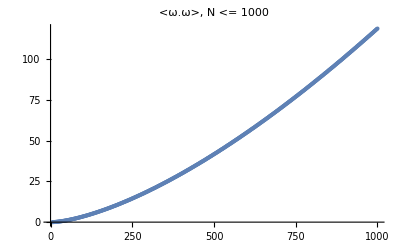

```mathematica
ListPlot[f2test,PlotLabel->"<ω.ω>, N <= 1000"]
```

```mathematica
f2test[[10]]
```

{24,0.317981016022237209}

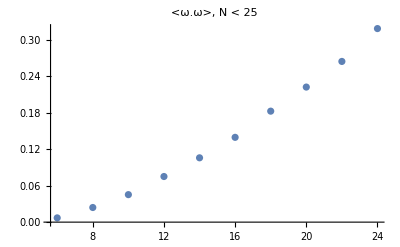

```mathematica
ListPlot[f2test[[;;10]],PlotLabel->"<ω.ω>, N < 25"]
```

```mathematica
f2model = LinearModelFit[Log[f2test[[-200;;]]],{x},x]
```

FittedModel[-«59»+«59» x]

```mathematica
Normal[f2model]
```

-5.6556773224669291+1.5105218612351004 x

```mathematica
f2meanmodel = NonlinearModelFit[Log[f2test[[-200;;]]],{a + b Log[x]+ 1.5 x},{a, b},x]
```

FittedModel[«1»]

```mathematica
Normal[f2meanmodel]
```

-5.71855+1.5 x+0.070124 Log[x]

```mathematica
ShowLogFitModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[model[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{model[Log[N]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"Log[N]", "Log[<ω.ω>]"}
];
```

```mathematica
ShowFitLogModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{Exp[model[Log[N]]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<ω.ω>"}
];
```

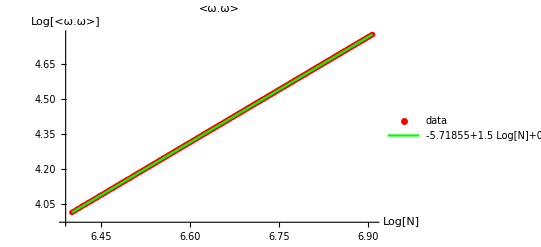

```mathematica
ShowLogFitModel[Log[f2test[[-200;;]]],f2meanmodel,"<ω.ω>"]
```

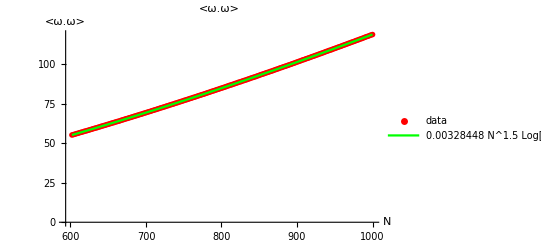

```mathematica
ShowFitLogModel[f2test[[-200;;]],f2meanmodel,"<ω.ω>"]
```

```mathematica
f2meanmodel["ParameterTable"]
```

General::munfl: Exp[-1059.1] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -5.71855 | 0.00195984 | -2917.87 | 0.
b | 0.070124 | 0.00103242 | 67.9219 | 3.86518×10^-139

```mathematica
Exp[f2meanmodel[Log[N]]]
```

0.00328448 N^1.5 Log[N]^0.070124

```mathematica
N^2/2 1/4Integrate[Exp[-ω^2/2 N+ I  ω z Sqrt[N]]ω^2/(2 Pi),{ω,-Infinity,Infinity},GenerateConditions->False]
```

-(ⅇ^(-z^2/2) √N (-1+z^2))/(8 √(2 π))

```mathematica
Sqrt[N]Integrate[(ⅇ^(-z^2/2) (1-z^2))/(8 √(2 π))E^(-z^2/2)/Sqrt[2 Pi],{z,-Infinity,Infinity}]
```

(√N)/(32 √π)

```mathematica
FullSimplify[Integrate[(√N)/(32 √π)Cot[Pi y]^2,{y,1/q,1-1/q},GenerateConditions->False],q > 2]
```

(√N (-π (-2+q)+2 q Cot[π/q]))/(32 π^(3/2) q)

```mathematica
Asymptotic[(√N (-π (-2+q)+2 q Cot[π/q]))/(32 π^(3/2) q),{q, Infinity,1}]
```

(√N q)/(16 π^(5/2))

```mathematica
Integrate[2 x (√N N x)/(16 π^(5/2)),{x,0,1}]
```

N^(3/2)/(24 π^(5/2))

```mathematica
SP[q_]:=
Block[{betas, ints},
betas =Select[Range[q-1],GCD[#,q]==1&]2 Pi/q;
ints = Cot[#/2]^2& /@ betas;
(Plus @@  ints)
];
```

```mathematica
SSP[M_] := Sum[N[SP[q],20],{q,2,M}]/Sum[EulerPhi[q],{q,2,M}]
```

```mathematica
sspdata = ParallelTable[{q,SSP[q],20},{q,2,1000}];
```

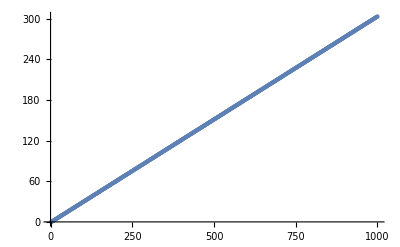

```mathematica
ListPlot[sspdata]
```

```mathematica
sspdata[[;;4]]
```

{{2,0},{3,0.22222222222222222222},{4,0.53333333333333333333},{5,0.74074074074074074074}}

```mathematica
data = sspdata[[-100;;]];
```

```mathematica
data[[;;10]]
```

{{901,273.08061947129422459},{902,273.45212079103667708},{903,273.84807231554604177},{904,274.17464424494350976},{905,274.43125264983876943},{906,274.83108843728250691},{907,274.92817164799914815},{908,275.25259047565902843},{909,275.56691465827922186},{910,276.01924204812497931}}

```mathematica
lmsp = NonlinearModelFit[data,{a + 3 x/Pi^2},{a},x]
```

FittedModel[-«44»+(3 x)/π^2]

```mathematica
""
```

```mathematica
Normal[lmsp[x]]
```

-0.71537026550465380233+(3 x)/π^2

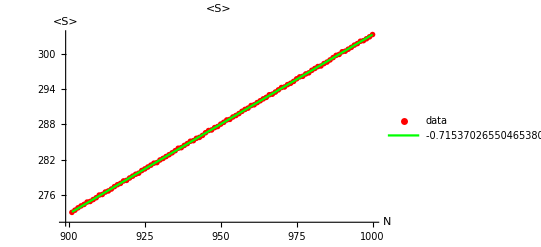

```mathematica
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[lmsp[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{lmsp[N]},PlotRange->All],
PlotLabel->"<S>",
AxesLabel->{"N", "<S>"}
]
```

```mathematica
N[lmsp["ParameterTable"],4]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.7154 | 0.0075 | -95.38 | 3.089×10^-99

```mathematica
(√N)/(32 √π)(3 N)/π^2
```

(3 N^(3/2))/(32 π^(5/2))

```mathematica
Sum[Cot[Pi p/q]^2,{p,1,q-1}]
```

1/3 (-2+q) (-1+q)

```mathematica
FactorInteger[24]
```

{{2,3},{3,1}}

```mathematica
21Times @@((1 -1/#[[1]])^#[[2]] &  /@FactorInteger[21])
```

12

```mathematica
S[q_] := q^2/3 Times @@ ((1 -1/#[[1]]^2)^#[[2]] &  /@FactorInteger[q]);
```

```mathematica
MB[N_] := Sum[S[q],{q,2,N}]/(N Sum[EulerPhi[q],{q,2,N}]) - 1/N
```

```mathematica
MB[1000]
```

4592457/16899500

```mathematica
MBT=ParallelTable[N[Pi^2MB[M],10],{M,1000000,1000005}]
```

FactorInteger::exact: Argument q in FactorInteger[q] is not an exact number.

Part::partd: Part specification q⟦1⟧ is longer than depth of object.

Part::partd: Part specification q⟦2⟧ is longer than depth of object.

FactorInteger::exact: Argument (1-1/q⟦1⟧^2)^q⟦2⟧ in FactorInteger[(1-1/q⟦1⟧^2)^q⟦2⟧] is not an exact number.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
Mean[MBT]
```

2.692772319

```mathematica
Sqrt[Variance[MBT]]
```

9.633×10^-6

```mathematica
Max[MBT] - Min[MBT]
```

0.00002204

```mathematica
1/4(MBT[[6]] +MBT[[4]])+ 1/4 (MBT[[5]] +MBT[[3]])
```

2.692776829

```mathematica
1/4Abs[MBT[[6]] -MBT[[4]]]+ 1/4 Abs[MBT[[5]] -MBT[[3]]]
```

0.000013